基礎庫 :

```mathematica
<<(FileNameJoin[{$UserDocumentsDirectory,"Wolfram Mathematica","snslib.wl"}])
```

WorkPath :

```mathematica
SetDirectory["D:\\Work\\SSR\\basePlan"];
dataPath = FileNameJoin[{ParentDirectory[],"_data"}]
```

D:\Work\SSR\_data

```mathematica
Config :
```

```mathematica
ClearAll[expconfig,heroconfig,drawconfig,pbconfig,skillconfig];
expconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"hero","exp"];
heroconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"hero","hero"];
drawconfig= Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"hero","draw"];
pbconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"hero","pb"];
skillconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"hero","skill"];
```

## 经验数值尺度

令：Tv(exp)与Tv(Lv)*lv成反比，则expSpeed与lv成线性 = (lv*step + Tv(lv+1))/(tvPara * step)
Tv(exp) =  tvPara / (Lv*Tv(Lv))

```mathematica
ClearAll[tvPara,expSpeed,expByLv];
tvPara[type_]:= getDayByLv[maxLv]*maxLv/expconfig[SelectFirst[#type==type&],"total"];
expSpeed[type_,lv_Integer]:= Module[{step=funcsLTStep/.Private`x->lv},(lv*step+getDayByLv[lv+1])/(tvPara[type]* step)];
expByLv[type_,lv_Integer]:= Sum[expSpeed[type,n]*funcsLTStep/.Private`x->n,{n,1,lv-1}];
expByLv[type_,lv_Real]:= expByLv[type,IntegerPart@lv]+(expByLv[type,IntegerPart@lv+1]-expByLv[type,IntegerPart@lv])*FractionalPart[lv];
```

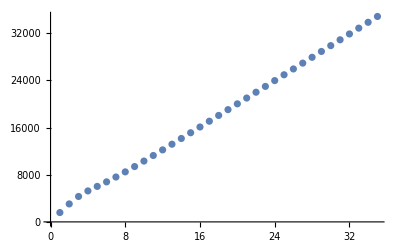

```mathematica
ListPlot@Table[expSpeed["hero",n],{n,1,maxLv}]
```

## 升级经验-Hero

```mathematica
ClearAll[x,heroExp];
heroExp[lv_]:= Round[expByLv["hero",excleInterpolation[lvconfig,"heroLv"->(lv+1),"Lv"]]-excleInterpolation[lvconfig,"heroLv"->(lv),"Lv"],10];
```

```mathematica
Export[FileNameJoin[{dataPath,"heroExp.txt"}],Prepend[Reverse@(Outer[Round[Times[#1,#2],5]&,Normal@heroconfig[;;-2,All][Normalize[#,Dot[#,Normal@heroconfig[;;-2,"standard"]]&]&,"lv_value"],Base`incrementSmooth@Table[heroExp[n],{n,1,lvconfig[Last,"heroLv"]-1}]]),Base`incrementSmooth@Table[heroExp[n] ,{n,1,lvconfig[Last,"heroLv"]-1}]],"Table"]
```

D:\Work\SSR\_data\heroExp.txt

## 升级经验-Commander

```mathematica
ClearAll[commanderExp];
commanderExp[lv_]:= expByLv["commander",excleInterpolation[lvconfig,"commanderLv"->(lv+1),"Lv"]]-expByLv["commander",excleInterpolation[lvconfig,"commanderLv"->(lv),"Lv"]];
```

```mathematica
Export[FileNameJoin[{dataPath,"commanderExp.txt"}],Base`incrementSmooth@Table[Round[commanderExp[n],5],{n,1,lvconfig[Last,"commanderLv"]-1}]]
```

D:\Work\SSR\_data\commanderExp.txt

## 抽卡

```mathematica
ClearAll[drawHero,drawShap,drawShapForHero,epHero,epSpecialHero,pbHeroGroup,epHeroGroup,heroSim,drawSim,infoSim,runSim,epSim];
(*抽到英雄的概率*)
drawHero[rank_] := <|rank->(drawconfig[Select[#item== rank<>"-hero"&]][Total,"pb"])|>;
drawHero = Merge[drawHero/@Normal[heroconfig[All,"rank"][[;;-2]]],First];
(*抽到英雄碎片的概率*)
drawShap[rank_] := <|rank->(drawconfig[Select[StringTake[#item,1]==rank&]][Total,#pb*#shap&])|>;
drawShap = Merge[drawShap/@Normal[heroconfig[All,"rank"][[;;-2]]],First];
(*抽到英雄碎片的概率-排除英雄转化*)
drawShapForHero[rank_] := <|rank->(drawconfig[Select[And[StringTake[#item,1]==rank,#shap≠10]&]][Total,#pb*#shap&])|>;
drawShapForHero = Merge[drawShapForHero/@Normal[heroconfig[All,"rank"][[;;-2]]],First];
(*抽到英雄的期望次数*)
epHero[rank_] := <|rank->Min[1/drawHero[rank],If[drawShapForHero[rank]>0,10/drawShapForHero[rank],Infinity]]|>;
epHero = Merge[epHero/@Normal[heroconfig[All,"rank"][[;;-2]]],First];
(*抽到特定英雄的期望次数*)
epSpecialHero[id_]:= Module[{rank= pbconfig[SelectFirst[#id==id&],"rank"]},epHero[rank]/pbconfig[Select[#rank==rank&],All][Normalize[#,Total]&,"weight"][[Base`excleIndex[pbconfig[Select[#rank==rank&],All],"id"->id]]]];
(*n次内抽到特定英雄的概率*)
pbHeroGroup[n_,id_]:=Module[{p=1/epSpecialHero[id]},Sum[(1-p)^(x-1)*p,{x,1,n}]];
(*epHeroGroup[result_List]:= Sum[n*pbHeroGroup[n,result],{n,Length@result,Infinity}];*)
(*抽卡模拟*)
heroSim[rank_,n_]:= Module[{pool=Accumulate[Normalize[Normal@pbconfig[Select[#rank==rank&],"weight"],Total]],r=RandomReal[1,n]},Counts@Part[pbconfig[Select[#rank==rank&],"id"],Flatten[FirstPosition[pool,x_/;x≥#]&/@r]]];
shardSim[rank_,num_,n_]:= Module[{pool=Accumulate[Normalize[Normal@pbconfig[Select[#rank==rank&],"weight"],Total]],r=RandomReal[1,n]},Counts@Part[pbconfig[Select[#rank==rank&],"id"],Flatten[FirstPosition[pool,x_/;x≥#]&/@r]]][KeyMap["shard_"<>#&],num*#&];
drawSim[n_]:= Module[{pool=Accumulate[Normal@drawconfig[All,"pb"]],r=RandomReal[1,n]},Counts@Part[drawconfig[All,"item"],Flatten[FirstPosition[pool,x_/;x≥#]&/@r]]]//Normal;
infoSim[key_/;key=="other",n_Integer]:= <|key->n|>;
infoSim[key_/;StringLength[key]>2,n_Integer]:= heroSim[StringTake[key,1],n]//Normal;
infoSim[key_/;NumberQ@ToExpression[StringTake[key,-1]],n_Integer]:= shardSim[StringTake[key,1],ToExpression[StringTake[key,-1]],n]//Normal;
runSim[base_Association]:= Merge[{First@KeyValueMap[infoSim,drawSim[1]],base},Total];
epSim[result_List]:= N@Mean@Array[Length@NestWhile[runSim,<||>,!ContainsAll[Keys[#],result]&]&,1000];
(*runSim[n_Integer]:= Merge[KeyValueMap[infoSim,drawSim[n]],Total];
epSim[result_List]:= N@Mean@Array[Module[{n=1},While[!ContainsAll[Keys@runSim[n],result],n++];n]&,10000];*)
```

## 升星

## 技能升级

```mathematica
ClearAll[skillPut,skillDay,skillNum,skillLvUp];
skillPut[day_]:=AssociationMap [1/Base`excleLookUp[skillconfig,"rank"->#,"tValue"]&,skillconfig[All,"rank"][DeleteCases[x_/;x==""]]][All,day*#&];
skillDay = Differences[Base`excleLookUp[skillconfig,"skillLv"->#,"Day"]&/@{1,2,3,4,5}];
skillNum = AssociationMap [4*Base`excleLookUp[heroconfig,"rank"->#,"standard"]&,skillconfig[All,"rank"][DeleteCases[x_/;x==""]]];
skillLvUp =Dataset[Merge[{Normal@#,Normal@skillNum},Apply[Divide]]&/@(skillPut/@skillDay)][All,All,Round]
```

```mathematica
snsUpdateTable["C:\\k-config\\excel\\se_npc.csv",snsDataFromExcle["D:\\Work\\SSR\\basePlan\\工作计划.xlsx","test"]]
```

C:\k-config\excel\se_npc.csv

```mathematica
snsDeleteData["C:\\k-config\\excel\\se_npc.csv",{1,2}]
```

C:\k-config\excel\se_npc.csv

```mathematica
Dataset[snsTable["enum_string.csv"]][Select[#枚举Type=="Quality"&],{"枚举Key(英文或者中文)","枚举Value"}]
```

```mathematica
expByDay["hero",360]
```

129599999

```mathematica
1/expValue["hero",12.8]
```

3973.